```mathematica
Clear["Global`*"]
```

```mathematica
a=2.46;(*a is given in units of 10^-10*)
γ0=3.1;
γ1=0.38;
γ2=-0.015;
γ3=0.29;
γ4=0.141;
δ=-0.0105;
Δ1=0.05;
Δ2=-0.0023;
(*γ1=0.;
γ2=0.;
γ3=0.;
γ4=0.;
δ=0.;
Δ1=0.;
Δ2=0.;*)
u[kx_,ky_]=1.+2.*Cos[0.5*kx*a]*Exp[-ⅈ*ky*a*0.5*√3];
v[kx_,ky_]=Exp[ⅈ*ky*a*√3]*u[kx,ky];
Hk[kx_,ky_]={{Δ1+Δ2,-γ0*u[kx,ky],γ4*u[kx,ky]*,γ1,0,0},{-γ0*u[kx,ky]*,Δ1+Δ2+δ,γ3*v[kx,ky],γ4*u[kx,ky]*,0.5*γ2,0},{γ4*u[kx,ky],γ3*v[kx,ky]*,-2.*Δ2,-γ0*u[kx,ky],γ4*v[kx,ky]*,γ1},{γ1,γ4*u[kx,ky],-γ0*u[kx,ky]*,-2.*Δ2,γ3*u[kx,ky],γ4*u[kx,ky]*},{0,0.5*γ2,γ4*v[kx,ky],γ3*u[kx,ky]*,Δ2-Δ1+δ,-γ0*v[kx,ky]},{0,0,γ1,γ4*u[kx,ky],-γ0*v[kx,ky]*,Δ2-Δ1}};
(*Number of bands*)
Nb=Length[Hk[kx,ky]];
```

```mathematica
μ=-0.052175;(*0.065*γ0;Chemical potential. VHS is at μ=-0.052175;*)
kbT=0.0000861*0.1*1000; (*Boltzmann's k × temperature*)
η=0.001;(*Self energy*)
```

```mathematica
Nk=50;(*k-mesh will have Nk^2 points, Nk>1, integer*)
StringForm["The k-mesh has `` points.",Nk^2]
Λk=1; (*A factor controlling the size of the mesh in k space*)
Δk=Λk/Nk; (*Spacing between k-points*)

b=(4π)/(√3*a); (*Magnitude of reciprocal vectors*)
b1=b*{(-√3)/2,1/2}; (*Reciprocal vectors b1,b2*)
b2=b*{(√3)/2,1/2};
lineb1=Arrow[{{0,0},b1}]; 
lineb2=Arrow[{{0,0},b2}]; 
BZcontour = Polygon[{(4π)/(3a)*{-1,0},(4π)/(3a)*{-1/2,(√3)/2},(4π)/(3a)*{1/2,(√3)/2},(4π)/(3a)*{1,0},(4π)/(3a)*{1/2,(-√3)/2},(4π)/(3a)*{-1/2,(-√3)/2}}];
kaMesh=Flatten[Table[{(j-i)*Δk*b*(√3)/2,(j+i)*Δk*b*1/2},{i,1,Nk,1},{j,1,Nk,1}],1]; (*k-mesh first generated by reciprocal vectors *)
kaMesh1BZ=kaMesh-TensorProduct[(1-UnitStep[kaMesh.b2])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b1/b^2+0.5],b1]-TensorProduct[(1-UnitStep[kaMesh.b1])*UnitStep[kaMesh.(b1+b2)]*Floor[kaMesh.b2/b^2+0.5],b2]-TensorProduct[UnitStep[kaMesh.b1]*UnitStep[kaMesh.b2]*Floor[kaMesh.(b1+b2)/b^2+0.5],(b1+b2)]; (*Moving all k-points to 1BZ*)
(*Increasing covered area of the 1BZ*)
kaMesh1BZ=kaMesh1BZ*1.0;
(*MOVING K MESH TO K POINT*)
kaMesh1BZ=(kaMesh1BZᵀ-0.0*{(4π)/(3a),0})ᵀ;
kaMeshKpoint= kaMesh1BZ;
kaMesh1BZ=kaMesh1BZ-1*TensorProduct[UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]]*Floor[kaMesh1BZ.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kaMesh1BZ[[All,1]]*kaMesh1BZ[[All,2]]])*Floor[kaMesh1BZ.b1/b^2+0.5],b1];

qaMesh1BZKpΓK=DeleteCases[kaMesh1BZ,{kx_,ky_}/; ky≠0]; (*Defining q-path as all points with ky=0. This is K'->Γ->K *)
```

The k-mesh has 2500 points.

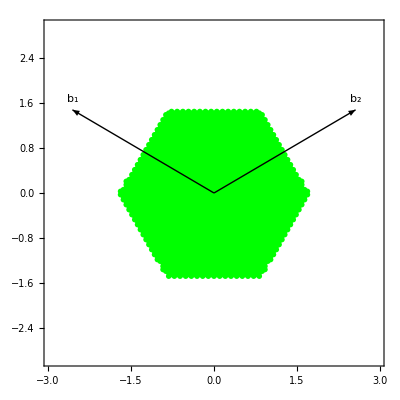

```mathematica
Show[ListPlot[{kaMesh1BZ},AspectRatio->Automatic,Epilog->{lineb1,lineb2,Text["b_1",b1+{0,0.2}],Text["b_2",b2+{0,0.2}]},AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-b,b},{-b,b}},Frame->True], Graphics[{Red,Opacity[0.],EdgeForm [Dashed],BZcontour}] ]
```

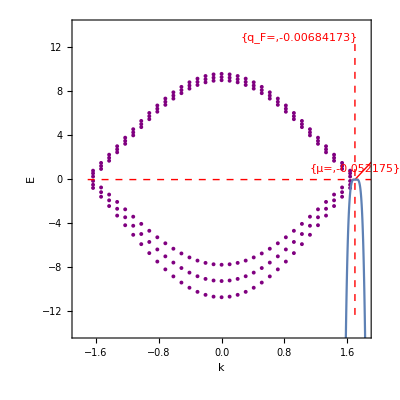

```mathematica
Eψk=Map[Eigensystem,Apply[Hk,kaMeshKpoint,{1}]];
Enkp=Eψk[[All,1]];
(*EsurfKp=Flatten[Table[Flatten[{kaMesh1BZ[[i]],Enkp[[i,j]]}],{i,Nk^2},{j,Nb}],1];
ListPointPlot3D[EsurfKp,AspectRatio->1]
ListPlot[{kaMesh1BZ},AspectRatio->Automatic,AspectRatio->Automatic,PlotMarkers->{Graphics[{Green,Disk[{0,0}]}],0.01},PlotStyle->Blue,PlotRange->{{-ba,ba},{-ba,ba}},Frame->True]
*)
iqp=Flatten[Position[kaMeshKpoint ,{kx_,ky_} /; ky==0]];
EpathKp=Flatten[Table[Flatten[{kaMeshKpoint [[iqp[[i]]]][[1]],Enkp[[iqp[[i]],j]]}],{i,Length[iqp]},{j,Nb}],1];
EF=Line[{{-(4π)/(3a),μ},{2*(4π)/(3a),μ}}]; (*Fermi level*)
qF=Line[{{(4π)/(3.*a)+μ/(1*γ0*a),-4*γ0},{(4π)/(3.*a)+μ/(1*γ0*a),4*γ0}}];
Dirac=Line[{{(4π)/(3.*a)+0,0},{(4π)/(3.*a)+1,γ0*a*1}}];
(*To visualize μ better:
δK  = 0.3/a;
δE = 0.02*γ0;
*)
(*Fuller view *)
δK  = 4.5/a;
δE = 4.5*γ0;
k0= (4π)/(3a)*0;

Show[ListPlot[EpathKp,PlotRange->{{k0-δK,k0+δK},{-δE,δE}},Joined->False,AspectRatio->1,PlotMarkers->{Automatic, Tiny},PlotStyle->Purple,Frame->True,FrameLabel->{"k","E"}],Graphics[{Red,Dashed,EF}],Graphics[{Red,Dashed,qF}],Graphics[{Red,Thick,Dirac}],Graphics[{Red,Text[{Style["μ=",Medium],μ},{(4π)/(3a),μ+1}]}],Graphics[{Red,Text[{Style["q_F=",Medium],μ/(γ0*a)},{μ/(γ0*a)+1,4*γ0+0.5}]}],Plot[-0.007*(((k-(4π)/(3a))/0.018)^2-1)^2+μ+.004,{k,0,10}]]
```

```mathematica
(*Defining parameters for sampling in q*)
Nq=50;
Lq=(4π)/(3a);
Δq=Lq/Nq;

qi=Table[{i*Δq,0.},{i,0,Nq}];
ω=0.;
```

General::munfl: 1/(9.26221×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.75581×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1/(1.59213×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.74726×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

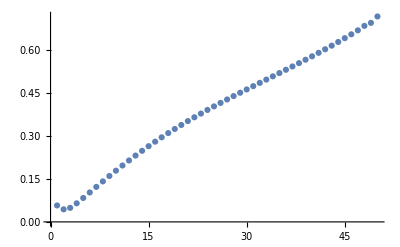

```mathematica
(*Calculating polarizability for q-path*)
Eψk=Map[Eigensystem,Apply[Hk,kaMesh1BZ,{1}]];
Enk=Eψk[[All,1]];
ψnk=Eψk[[All,2]];
ψnk=Map[Normalize,ψnk,{2}];
kqaMesh1BZ=kaMesh1BZ; (*Starting with q={0.,0.}*)
Πq0=Table[0,{i,0,Nq}];
Πq0[[1]] = -(2/Nk^2)*Total[Map[-1/(2*kbT*(1+Cosh[(#-μ)/kbT]))&,Enk],2];
For[i=1,i≤Nq,i++,
q={i*Δq,0.}; (*Not being used*)
kqaMesh = (kqaMesh1BZᵀ+{Δq,0})ᵀ;
kqaMesh1BZ = kqaMesh-1*TensorProduct[UnitStep[kqaMesh.(b1+b2)]*Floor[kqaMesh.b2/b^2+0.5],b2]-1*TensorProduct[(1-UnitStep[kqaMesh.(b1+b2)])*Floor[kqaMesh.b1/b^2+0.5],b1];
Eψkq=Map[Eigensystem,Apply[Hk,kqaMesh1BZ,{1}]];
Enkq= Eψkq[[All,1]];
ψnkq=Eψkq[[All,2]];
ψnkq=Map[Normalize,ψnkq,{2}];
nfEk=Map[1/(1+Exp[(#-μ)/kbT])&,Enk];
nfEkq=Map[1/(1+Exp[(#-μ)/kbT])&,Enkq];
Δnf=Table[Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,1]]-Tuples[{nfEk[[i]],nfEkq[[i]]}][[All,2]],{i,Nk^2}];
ΔE=Table[Tuples[{Enk[[i]],Enkq[[i]]}][[All,1]]-Tuples[{Enk[[i]],Enkq[[i]]}][[All,2]],{i,Nk^2}]+ω+ⅈ*η;(*+ⅈ*η*)
ψTuples=Table[Tuples[{ψnk[[i]],ψnkq[[i]]*}],{i,Nk^2}];
Fkq=Table[Abs[ψTuples[[i]][[j]][[1]].ψTuples[[i]][[j]][[2]]]^2,{i,Nk^2},{j,Nb^2}];
Πq0[[i+1]]=-(2/Nk^2)*Total[Flatten[(Δnf/ΔE)*Fkq]](**((ω)/Norm[q]^2) *)

]
ListPlot[Table[{i,Re[Πq0[[i]]]},{i,1,Nq}]]
```

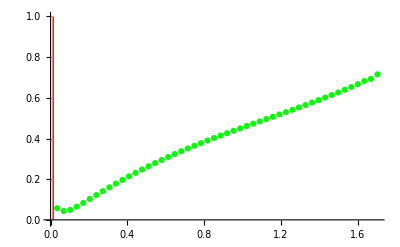

```mathematica
Show[ListPlot[Table[{qi[[i+1,1]],Re[Πq0[[i]]]},{i,0,Nq}],PlotRange->{-.01,1},PlotStyle-> Green],Graphics[{Red,Line[{{-2*μ/(γ0*a),0},{-2*1μ/(γ0*a),1}}]}]]
```